```mathematica
Clear["Global`*"]
```

# Parameters

```mathematica
Subscript[ρ, max]=1 (*maximum carbon uptake rate (d^-1)*);
Subscript[α, max]=1.5*10^-9(*attack rate of mixotroph on bacteria (cm^2*d^-1*Subscript[cell, M]^-1)*);
b=.15(*conversion rate of bacteria to mixotroph (Subscript[cell, M]*Subscript[cell, B]^-1)*);
Subscript[K, B]=1 10^8; (*carrying capacity of bacteria (Subscript[cell, B]*cm^-2)*);
r=.693(*growth rate of bacteria (d^-1)*);
h=250(*half saturation constant for photosynthesis (µmol quanta*m^2*s^-1)*);
Subscript[I, in]=100(*incident light (µmol quanta*m^2*s^-1)*);
k=5*10^(-7)(*mixotroph light absorbance constant (cm^2*Subscript[cell, M]^-1)*);
l=.05(*mixotroph mortality rate (d^-1)*);
Subscript[m, ρ]=.1;(*photosynthetic temeprature sensitivity coefficient (^o C^-1)*);
Subscript[m, α]=.25;(*heterotrophic temperature sensitivity coefficient (^o C^-1)*);
T0=13; (*baseline temperature (^o C)*);
T0α=T0 - 1/Subscript[m, α] (*minmimum temperature for heterotrophy (^o C)*);
T0ρ=T0 - 1/Subscript[m, ρ] (*minmimum temperature for photosynthesis (^o C)*);
Subscript[k, b]=8.62*10^-5(*Boltzmann constant (eV*K^-1)*);
Subscript[E, aρ]=.5 (*photosynthetic activation energy (eV)*);
Subscript[E, aα]=.85 (*heterotrophic activation energy (eV)*);
r0ρ=6.4279909706*^8 (*photosynthetic normalization constant*);
r0α=9.412997398*^14 (*heterotrophic normalization constant*);
```

# Equations/Functions for generating outputs

## Equations

```mathematica
(*temperature-dependent photosynthetic rate*)
ρ[θ_,z_,T_]:=Subscript[ρ, max]*(1-θ^(2^z))^(1/2^z)(Subscript[m, ρ] (T-T0ρ))
ρExp[θ_,z_,T_]:=Subscript[ρ, max]*(1-θ^(2^z))^(1/2^z)r0ρ E^((-Subscript[E, aρ])/(Subscript[k, b](273+T)))

(*temperature-dependent grazing rate*)
α[θ_,T_]:=Subscript[α, max]*θ (Subscript[m, α] (T-T0α))
αExp[θ_,T_]:=Subscript[α, max]*θ r0α E^((-Subscript[E, aα])/(Subscript[k, b](273+T)))

(*solves for mixotroph and bacteria population density at equilibrium*)
eqs[θ_,z_,T_]:=FindRoot[{dM[θ, z,T] ==0,dB[θ,T]==0 },{{M,10^7},{B,10^7}},AccuracyGoal->Infinity]
eqsExp[θ_,z_,T_]:=FindRoot[{dMExp[θ, z,T] ==0,dBExp[θ,T]==0 },{{M,10^7},{B,10^7}},AccuracyGoal->Infinity]

(*mixotroph per capita  growth rate*)
dM[θ_, z_,T_]:=(ρ[θ,z,T]/(k M) Log[(h+Subscript[I, in])/(h+Subscript[I, in]* Exp[-k M ])]-l+ α[θ,T] b B) 
dMExp[θ_, z_,T_]:=(ρExp[θ,z,T]/(k M) Log[(h+Subscript[I, in])/(h+Subscript[I, in]* Exp[-k M ])]-l+ αExp[θ,T] b B)

(*bacteria per capita growth rate*)
dB[θ_,T_]:=(r(1-(B/Subscript[K, B]))-α[θ,T]  M) 
dBExp[θ_,T_]:=(r(1-(B/Subscript[K, B]))-αExp[θ,T]  M)

(*mutant fitness equation*)
Fitness[θm_,z_,M_,B_,T_]:=-l+α[θm,T]  b B +(ρ[θm,z,T] Log[(h+Subscript[I, in])/(h+ ⅇ^(-(k M)) Subscript[I, in])])/(k M)
FitnessEmpty[θm_,θ_,z_,T_]:=-l+α[θm,T]  b Subscript[K, B] +(Subscript[I, in] ρ[θm,z,T])/(Subscript[I, in]+h)
FitnessExp[θm_,z_,M_,B_,T_]:=-l+αExp[θm,T]  b B +(ρExp[θm,z,T] Log[(h+Subscript[I, in])/(h+ ⅇ^(-(k M)) Subscript[I, in])])/(k M)

(*selection gradient*)
SelectionGrad[θm_,z_,M_,B_,T_]:=Subscript[α, max] (Subscript[m, α] (T-T0α)) b B -(ρ[θm,z,T] θm^(-1+2^z) (1-θm^(2^z))^-1  Log[(h+Subscript[I, in])/(h+ⅇ^(-k M) Subscript[I, in])])/(k M)
SelectionGradExp[θm_,z_,M_,B_,T_]:=b B ⅇ^(-Subscript[ⅇ, aα]/((273+T) Subscript[k, b])) r0α Subscript[α, max]-(ⅇ^(-Subscript[ⅇ, aρ]/((273+T) Subscript[k, b])) r0ρ θm^(-1+2^z) (1-θm^(2^z))^(-1+2^-z) Log[(h+Subscript[ⅈ, in])/(h+ⅇ^(-k M) Subscript[ⅈ, in])] Subscript[ρ, max])/(k M)
```

## Pairwise invasibility plots (PIP)

```mathematica
(*Uses a chosen shape parameter z, temperature T, and color to generate a pairwise invasibility plot using the fitness function for an invading mutant mixotroph. Regions in which mutant fitness is positive are shaded. Function has been modivfied to only shade regions in which resident is viable*)
MakePIP[z_,T_,color_]:=RegionPlot[If[(M/.eqs[θ,z,T])>0&&(B/.eqs[θ,z,T])>0,Fitness[θm,z,M/.eqs[θ,z,T],B/.eqs[θ,z,T],T],FitnessEmpty[θm,θ,z,T]]≥  0,{θ,0,1},{θm,0,1},PlotStyle->{color},BoundaryStyle->{color},Frame->True,FrameLabel->{Style["Resident Heterotrophic investment (θ_res)",12,Black],Style["Mutant Heterotrophic investment (θ_mut)",12,Black]},FrameTicksStyle->Directive[Black,12],ImageSize->Medium]
(*generates a RegionPlot without checking for viability. This is overlayed with a RegionPlot made using the function above to show regions with nonviable residents*)
MakePIPNV[z_,T_,color_]:=RegionPlot[(M/.eqs[θ,z,T])≤  0,{θ,0,1},{θm,0,1},PlotStyle->{color,Opacity[.4]},BoundaryStyle->None,Frame->True,FrameLabel->{Style["Resident Heterotrophic investment (θ_res)",12,Black],Style["Mutant Heterotrophic investment (θ_mut)",12,Black]},FrameTicksStyle->Directive[Black,12],ImageSize->Medium]

MakePIPexp[z_,T_,color_]:=RegionPlot[Fitness[θm,z,If[(M/.eqsExp[θ,z,T])≥0,M/.eqsExp[θ,z,T],0],If[(B/.eqsExp[θ,z,T])≥0,B/.eqsExp[θ,z,T],0],T]≥  0,{θ,0,1},{θm,0,1},PlotStyle->color,BoundaryStyle->{Bold,Dashed,Black},Frame->True,FrameLabel->{Style["Resident Heterotrophic investment (θ_res)",12,Black],Style["Mutant Heterotrophic investment (θ_mut)",12,Black]},FrameTicksStyle->Directive[Black,12],ImageSize->Medium]
MakePIPNVexp[z_,T_,color_,colorm_]:=RegionPlot[Fitness[θm,z,M/.eqsExp[θ,z,T],B/.eqsExp[θ,z,T],T]≥  0,{θ,0,1},{θm,0,1},PlotStyle->color,Mesh->20,MeshStyle->colorm,BoundaryStyle->{Bold,Dashed,Black},Frame->True,FrameLabel->{Style["Resident Heterotrophic investment (θ_res)",12,Black],Style["Mutant Heterotrophic investment (θ_mut)",12,Black]},FrameTicksStyle->Directive[Black,12],ImageSize->Medium]
```

## Generating ESS vs Temp plots for generalist and specialist mixotrophs

```mathematica
(*makeθListGen[], makeθListLin[], and makeθListSpec[] generate lists containing the evolutionarily stable investment strategy Subscript[θ, ESS] as a function of temperature for generalist tradeoff, linear, and specialist tradeoff mixotrophs respectively*)
```

```mathematica
makeθListGen[]:=
{
θESSgen = {};
Quiet[For[T=1,T<41,T++,
currentθ = θm/.FindRoot[SelectionGrad[θm,1,M/.eqs[θm,1,T],B/.eqs[θm,1,T],T]==0,{θm,.99}];
If[Re[currentθ] > 1, AppendTo[θESSgen, 1],(*if calculated Subscript[θ, ESS] > 1 (maximum heterotrophic investment), 1 is added to list*)If[Re[currentθ] < 0, AppendTo[θESSgen,0.],AppendTo[θESSgen,currentθ]]](*if calculate Subscript[θ, ESS] < 0 (minimum heterotrophic investment), 0 is added to list*)
]];
θESSgen
}
makeθListLin[]:=
{
θESSlin = {};
Quiet[For[T=1,T<41,T++,
currentθ = θm/.FindRoot[SelectionGrad[θm,0,M/.eqs[θm,0,T],B/.eqs[θm,0,T],T]==0,{θm,.5}];
(*getting around issue where FindRoot identifies the incorrect, evolutionarily unstable root in some cases*)
If[1/(.0001)(SelectionGrad[.0002,0,M/.eqs[.0002,0,T],B/.eqs[.0002,0,T],T]-SelectionGrad[.0001,0,M/.eqs[.0001,0,T],B/.eqs[.0001,0,T],T]) > 0,AppendTo[θESSlin,1],If[Re[currentθ] > 1, AppendTo[θESSlin, 1],If[Re[currentθ] < 0, AppendTo[θESSlin,0.000],AppendTo[θESSlin,currentθ]]]]
]];
θESSlin 
}

makeθListGenExp[]:=
{
θESSgen = {};
Quiet[For[T=1,T<41,T++,
currentθ = θm/.FindRoot[SelectionGradExp[θm,1,M/.eqsExp[θm,1,T],B/.eqsExp[θm,1,T],T]==0,{θm,.99}];
If[Re[currentθ] > 1, AppendTo[θESSgen, 1],(*if calculated Subscript[θ, ESS] > 1 (maximum heterotrophic investment), 1 is added to list*)If[Re[currentθ] < 0, AppendTo[θESSgen,0.],AppendTo[θESSgen,currentθ]]](*if calculate Subscript[θ, ESS] < 0 (minimum heterotrophic investment), 0 is added to list*)
]];
θESSgen
}
makeθListLinExp[]:=
{
θESSlin = {};
Quiet[For[T=1,T<41,T++,
currentθ = θm/.FindRoot[SelectionGradExp[θm,0,M/.eqsExp[θm,0,T],B/.eqsExp[θm,0,T],T]==0,{θm,.5}];
(*getting around issue where FindRoot identifies the incorrect, evolutionarily unstable root in some cases*)
If[1/(.0001)(SelectionGradExp[.0002,0,M/.eqsExp[.0002,0,T],B/.eqsExp[.0002,0,T],T]-SelectionGradExp[.0001,0,M/.eqsExp[.0001,0,T],B/.eqsExp[.0001,0,T],T]) > 0,AppendTo[θESSlin,1],If[Re[currentθ] > 1, AppendTo[θESSlin, 1],If[Re[currentθ] < 0, AppendTo[θESSlin,0.000],AppendTo[θESSlin,currentθ]]]]
]];
θESSlin 
}
makeθListGen[]:=
{
θESSgen = {};
Quiet[For[T=1,T<41,T++,
currentθ = θm/.FindRoot[SelectionGrad[θm,1,M/.eqs[θm,1,T],B/.eqs[θm,1,T],T]==0,{θm,.99}];
If[Re[currentθ] > 1, AppendTo[θESSgen, 1],(*if calculated Subscript[θ, ESS] > 1 (maximum heterotrophic investment), 1 is added to list*)If[Re[currentθ] < 0, AppendTo[θESSgen,0.],AppendTo[θESSgen,currentθ]]](*if calculate Subscript[θ, ESS] < 0 (minimum heterotrophic investment), 0 is added to list*)
]];
θESSgen
}
makeθListLin[]:=
{
θESSlin = {};
Quiet[For[T=1,T<41,T++,
currentθ = θm/.FindRoot[SelectionGrad[θm,0,M/.eqs[θm,0,T],B/.eqs[θm,0,T],T]==0,{θm,.5}];
(*getting around issue where FindRoot identifies the incorrect, evolutionarily unstable root in some cases*)
If[1/(.0001)(SelectionGrad[.0002,0,M/.eqs[.0002,0,T],B/.eqs[.0002,0,T],T]-SelectionGrad[.0001,0,M/.eqs[.0001,0,T],B/.eqs[.0001,0,T],T]) > 0,AppendTo[θESSlin,1],If[Re[currentθ] > 1, AppendTo[θESSlin, 1],If[Re[currentθ] < 0, AppendTo[θESSlin,0.000],AppendTo[θESSlin,currentθ]]]]
]];
θESSlin 
}
makeθListGenExp[]:=
{
θESSgen = {};
Quiet[For[T=1,T<41,T++,
currentθ = θm/.FindRoot[SelectionGradExp[θm,1,M/.eqsExp[θm,1,T],B/.eqsExp[θm,1,T],T]==0,{θm,.99}];
If[Re[currentθ] > 1, AppendTo[θESSgen, 1],(*if calculated Subscript[θ, ESS] > 1 (maximum heterotrophic investment), 1 is added to list*)If[Re[currentθ] < 0, AppendTo[θESSgen,0.],AppendTo[θESSgen,currentθ]]](*if calculate Subscript[θ, ESS] < 0 (minimum heterotrophic investment), 0 is added to list*)
]];
θESSgen
}
makeθListLinExp[]:=
{
θESSlin = {};
Quiet[For[T=1,T<41,T++,
currentθ = θm/.FindRoot[SelectionGradExp[θm,0,M/.eqsExp[θm,0,T],B/.eqsExp[θm,0,T],T]==0,{θm,.5}];
(*getting around issue where FindRoot identifies the incorrect, evolutionarily unstable root in some cases*)
If[1/(.0001)(SelectionGradExp[.0002,0,M/.eqsExp[.0002,0,T],B/.eqsExp[.0002,0,T],T]-SelectionGradExp[.0001,0,M/.eqsExp[.0001,0,T],B/.eqsExp[.0001,0,T],T]) > 0,AppendTo[θESSlin,1],If[Re[currentθ] > 1, AppendTo[θESSlin, 1],If[Re[currentθ] < 0, AppendTo[θESSlin,0.000],AppendTo[θESSlin,currentθ]]]]
]];
θESSlin 
}

makeθListSpec[]:=
{
θESSspec1viable= Table[Null,40];
θESSspec0={};
Quiet[For[T=1,T<41,T++,
If[eqs[1,-1,T][[1]][[2]]>0, θESSspec1viable[[T;;T]]=1];
AppendTo[θESSspec0,0];
]];
θESSspec=Table[θESSspec1viable,θESSspec0];
θESSspec
}

makeθListSpecExp[]:=
{
θESSspec1viable= Table[Null,40];
θESSspec0={};
Quiet[For[T=1,T<41,T++,
If[eqsExp[1,-1,T][[1]][[2]]>0 ,θESSspec1viable[[T;;T]]=1];
AppendTo[θESSspec0,0];
]];
θESSspec=Table[θESSspec1viable,θESSspec0];
θESSspec
}
```

## Comparing evolved vs unevolved mixotrophs for carbon cycling

```mathematica
(*generates plots comparing mixotroph and bacteria populations, and growth rate components derived from photosynthesis, P(θ,z,I,T,M^*), and heterotrophy, G(θ,T,B^*), between evolving mixotrophs whos heterotrophic investment θ varies as a function of temperature and genetically static mixotrophs with fixed θ. This allows evolutionary and strictly thermal responses to be compared. Function inputs consist of the shape parameter, z, the chosen lower bounds for each set of plots (l1, l2, and l3) and the chosen upper bounds for each set of plots (u1, u2, and u3)*)
Ccycling[z_,l1_,u1_,l2_,u2_,l3_,u3_]:=
{makeθListLin[];
makeθListGen[];
θList=List[];
If[z ==0,θList=θESSlin,θList=θESSgen];

Mpopsevo=List[];
Mpopsnoevo=List[];
Quiet[For[t=1,t<100,t++,AppendTo[Mpopsevo,M/.eqs[θList[[t]],z,t]]]];
Quiet[For[t=1,t<100,t++,AppendTo[Mpopsnoevo,M/.eqs[θList[[T0]],z,t]]]];

bpopsevo=List[];
bpopsnoevo=List[];
Quiet[For[t=1,t<100,t++,AppendTo[bpopsevo,B/.eqs[θList[[t]],z,t]]]];
Quiet[For[t=1,t<100,t++,AppendTo[bpopsnoevo,B/.eqs[θList[[T0]],z,t]]]];

photgrowthevo=List[];
photgrowthnoevo=List[];
Quiet[For[t=1,t<100,t++,AppendTo[photgrowthevo,(M/.eqs[θList[[t]],z,t])*((ρ[θList[[t]],z,t]Log[(h+Subscript[I, in])/(h+ⅇ^(-(k (M/.eqs[θList[[t]],z,t]))) Subscript[I, in])])/(k (M/.eqs[θList[[t]],z,t])))]]];
Quiet[For[t=1,t<100,t++,AppendTo[photgrowthnoevo,(M/.eqs[θList[[T0]],z,t])*((ρ[θList[[T0]],z,t]Log[(h+Subscript[I, in])/(h+ⅇ^(-(k (M/.eqs[θList[[T0]],z,t]))) Subscript[I, in])])/(k (M/.eqs[θList[[T0]],z,t])))]]];


hetgrowthevo=List[];
hetgrowthnoevo=List[];
Quiet[For[t=1,t<100,t++,AppendTo[hetgrowthevo,(B/.eqs[θList[[t]],z,t])*(M/.eqs[θList[[t]],z,t]) α[θList[[t]],t] b]]];
Quiet[For[t=1,t<100,t++,AppendTo[hetgrowthnoevo,(B/.eqs[θList[[T0]],z,t])*(M/.eqs[θList[[T0]],z,t]) α[θList[[T0]],t] b]]];


List[ListPlot[{Mpopsevo,Mpopsnoevo},Joined->True,PlotRange->{{T0,33},{l1, u1}},PlotStyle->{{If[z>0,RGBColor["#B09771"],Black]},{If[z>0,RGBColor["#B09771"],Black],Dashed}},Frame->True,FrameLabel->{Style["Temperature (^oC)",15,Black], Style["M^*",15,Black]},FrameTicksStyle->Directive[Black,12],ImageSize->Medium],
ListPlot[{bpopsevo,bpopsnoevo},Joined->True,PlotRange->{{T0,33},{l2, u2}},PlotStyle->{{If[z>0,RGBColor["#B09771"],Black]},{If[z>0,RGBColor["#B09771"],Black],Dashed}},Frame->True,FrameLabel->{Style["Temperature (^oC)",15,Black], Style["B^*",15,Black]},FrameTicksStyle->Directive[Black,12],ImageSize->Medium],
ListPlot[{photgrowthevo,photgrowthnoevo,hetgrowthevo,hetgrowthnoevo},Joined->True,PlotRange->{{T0,33},{l3, u3}},PlotStyle->{{Darker[Green]},{Darker[Green],Dashed},{Black},{Black,Dashed}},Frame->True,FrameLabel->{Style["Temperature (^oC)",Black,15], Style["P(θ,z,I,T,M^*)*M, G(θ,T,B^*)*M",Black,12]},FrameTicksStyle->Directive[Black,12],ImageSize->Medium]]
}
Ccyclingspec[z_,l1_,u1_,l2_,u2_,l3_,u3_]:=
{makeθListSpec[];
θList0=Table[0,40];
θList1=Table[1,40];

Mpopsevo0=List[];
Mpopsnoevo0=List[];
Quiet[For[t=1,t<100,t++,AppendTo[Mpopsevo0,M/.eqs[θList0[[t]],z,t]]]];
Quiet[For[t=1,t<100,t++,AppendTo[Mpopsnoevo0,M/.eqs[θList0[[T0]],z,t]]]];

Mpopsevo1=List[];
Mpopsnoevo1=List[];
Quiet[For[t=1,t<100,t++,AppendTo[Mpopsevo1,M/.eqs[θList1[[t]],z,t]]]];
Quiet[For[t=1,t<100,t++,AppendTo[Mpopsnoevo1,M/.eqs[θList1[[T0]],z,t]]]];

bpopsevo0=List[];
bpopsnoevo0=List[];
Quiet[For[t=1,t<100,t++,AppendTo[bpopsevo0,B/.eqs[θList0[[t]],z,t]]]];
Quiet[For[t=1,t<100,t++,AppendTo[bpopsnoevo0,B/.eqs[θList0[[T0]],z,t]]]];

bpopsevo1=List[];
bpopsnoevo1=List[];
Quiet[For[t=1,t<100,t++,AppendTo[bpopsevo1,B/.eqs[θList1[[t]],z,t]]]];
Quiet[For[t=1,t<100,t++,AppendTo[bpopsnoevo1,B/.eqs[θList1[[T0]],z,t]]]];

photgrowthevo0=List[];
photgrowthnoevo0=List[];
Quiet[For[t=1,t<100,t++,AppendTo[photgrowthevo0,(M/.eqs[θList0[[t]],z,t])*((ρ[θList0[[t]],z,t]Log[(h+Subscript[I, in])/(h+ⅇ^(-(k (M/.eqs[θList0[[t]],z,t]))) Subscript[I, in])])/(k (M/.eqs[θList0[[t]],z,t])))]]];
Quiet[For[t=1,t<100,t++,AppendTo[photgrowthnoevo0,(M/.eqs[θList0[[T0]],z,t])*((ρ[θList0[[T0]],z,t]Log[(h+Subscript[I, in])/(h+ⅇ^(-(k (M/.eqs[θList0[[T0]],z,t]))) Subscript[I, in])])/(k (M/.eqs[θList0[[T0]],z,t])))]]];

photgrowthevo1=List[];
photgrowthnoevo1=List[];
Quiet[For[t=1,t<100,t++,AppendTo[photgrowthevo1,(M/.eqs[θList1[[t]],z,t])*((ρ[θList1[[t]],z,t]Log[(h+Subscript[I, in])/(h+ⅇ^(-(k (M/.eqs[θList1[[t]],z,t]))) Subscript[I, in])])/(k (M/.eqs[θList1[[t]],z,t])))]]];
Quiet[For[t=1,t<100,t++,AppendTo[photgrowthnoevo1,(M/.eqs[θList1[[T0]],z,t])*((ρ[θList1[[T0]],z,t]Log[(h+Subscript[I, in])/(h+ⅇ^(-(k (M/.eqs[θList1[[T0]],z,t]))) Subscript[I, in])])/(k (M/.eqs[θList1[[T0]],z,t])))]]];


hetgrowthevo0=List[];
hetgrowthnoevo0=List[];
Quiet[For[t=1,t<100,t++,AppendTo[hetgrowthevo0,(B/.eqs[θList0[[t]],z,t])*(M/.eqs[θList0[[t]],z,t]) α[θList0[[t]],t] b]]];
Quiet[For[t=1,t<100,t++,AppendTo[hetgrowthnoevo0,(B/.eqs[θList0[[T0]],z,t])*(M/.eqs[θList0[0[T0]],z,t]) α[θList0[[T0]],t] b]]];

hetgrowthevo1=List[];
hetgrowthnoevo1=List[];
Quiet[For[t=1,t<100,t++,AppendTo[hetgrowthevo1,(B/.eqs[θList1[[t]],z,t])*(M/.eqs[θList1[[t]],z,t]) α[θList1[[t]],t] b]]];
Quiet[For[t=1,t<100,t++,AppendTo[hetgrowthnoevo1,(B/.eqs[θList1[[T0]],z,t])*(M/.eqs[θList1[0[T0]],z,t]) α[θList1[[T0]],t] b]]];


List[ListPlot[{Mpopsevo1,Mpopsevo0,Mpopsnoevo1,Mpopsnoevo0},Joined->True,PlotRange->{{9,33},{l1, u1}},PlotStyle->{{Lighter[RGBColor["#287DAB"]]},{RGBColor["#287DAB"]},{Lighter[RGBColor["#287DAB"]],Dashed},{RGBColor["#287DAB"],Dashed}},Frame->True,FrameLabel->{Style["Temperature (^oC)",15,Black], Style["M^*",15,Black]},FrameTicksStyle->Directive[Black,12],ImageSize->Medium],
ListPlot[{bpopsevo1,bpopsevo0,bpopsnoevo1,bpopsnoevo0},Joined->True,PlotRange->{{9,33},{l2, u2}},PlotStyle->{{Lighter[RGBColor["#287DAB"]]},{RGBColor["#287DAB"]},{Lighter[RGBColor["#287DAB"]],Dashed},{RGBColor["#287DAB"],Dashed}},Frame->True,FrameLabel->{Style["Temperature (^oC)",15,Black], Style["B^*",15,Black]},FrameTicksStyle->Directive[Black,12],ImageSize->Medium],
ListPlot[{photgrowthevo0,photgrowthevo1,photgrowthnoevo0,photgrowthnoevo1,hetgrowthevo0,hetgrowthevo1,hetgrowthnoevo0,hetgrowthnoevo1},Joined->True,PlotRange->{{9,33},{l3, u3}},PlotStyle->{{Darker[Green]},{Darker[Green]},{Darker[Green],Dashed},{Darker[Green],Dashed},{Black},{Black},{Black,Dashed},{Black,Dashed}},Frame->True,FrameLabel->{Style["Temperature (^oC)",Black,15], Style["P(θ,z,I,T,M^*)*M, G(θ,T,B^*)*M",Black,12]},FrameTicksStyle->Directive[Black,12],ImageSize->Medium]]
}
```

# θ vs. Temperature plots

## I_in=100

## Linear temperature dependence

Table::nliter: Non-list iterator θESSspec0 at position 2 does not evaluate to a real numeric value.

General::stop: Further output of Table::nliter will be suppressed during this calculation.

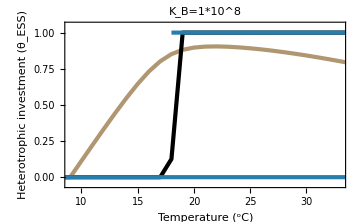
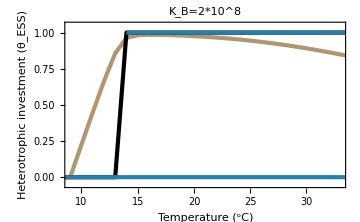
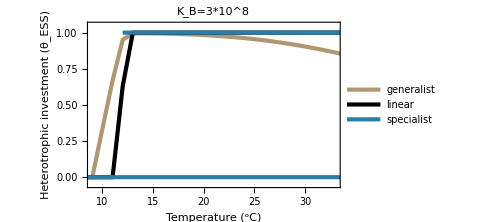

```mathematica
List[Subscript[K, B]=1 10^8;Subscript[I, in]=100;
ListPlot[{makeθListGen[]//Flatten,makeθListLin[]//Flatten,makeθListSpec[][[1]][[1]],makeθListSpec[][[1]][[2]]},Joined->True,PlotRange->{{9,33},{-.05,1.05}},PlotStyle->{{RGBColor["#B09771"],AbsoluteThickness[3]}, {Black,AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]}},Frame->True,ImageSize->Medium,FrameLabel->{Style["Temperature (^oC)",12,Black],Style["Heterotrophic investment (θ_ESS)",12,Black]},FrameTicksStyle->Directive[Black,12],PlotLabel->Style["K_B=1*10^8",12,Black]],Subscript[K, B]=2 10^8;Subscript[I, in]=100;
ListPlot[{makeθListGen[]//Flatten,makeθListLin[]//Flatten,makeθListSpec[][[1]][[1]],makeθListSpec[][[1]][[2]]},Joined->True,PlotRange->{{9,33},{-.05,1.05}},PlotStyle->{{RGBColor["#B09771"],AbsoluteThickness[3]}, {Black,AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]}},Frame->True,ImageSize->Medium,FrameLabel->{Style["Temperature (^oC)",12,Black],Style["Heterotrophic investment (θ_ESS)",12,Black]},FrameTicksStyle->Directive[Black,12],PlotLabel->Style["K_B=2*10^8",12,Black]],Subscript[K, B]=3 10^8;Subscript[I, in]=100;
ListPlot[{makeθListGen[]//Flatten,makeθListLin[]//Flatten,makeθListSpec[][[1]][[1]],makeθListSpec[][[1]][[2]]},Joined->True,PlotRange->{{9,33},{-.05,1.05}},PlotStyle->{{RGBColor["#B09771"],AbsoluteThickness[3]}, {Black,AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]}},Frame->True,ImageSize->Medium,FrameLabel->{Style["Temperature (^oC)",12,Black],Style["Heterotrophic investment (θ_ESS)",12,Black]},PlotLegends->{"generalist", "linear","specialist"},FrameTicksStyle->Directive[Black,12],PlotLabel->Style["K_B=3*10^8",12,Black]]]
```

## Exponential temperature dependence

Table::nliter: Non-list iterator θESSspec0 at position 2 does not evaluate to a real numeric value.

General::stop: Further output of Table::nliter will be suppressed during this calculation.

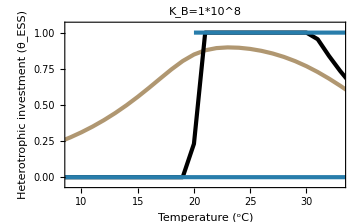
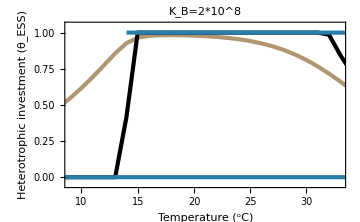
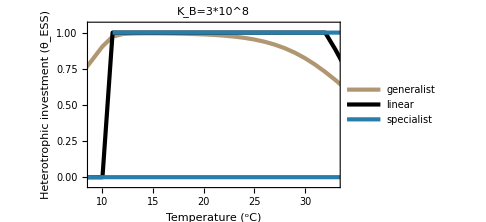

```mathematica
List[Subscript[K, B]=1 10^8;Subscript[I, in]=100;
ListPlot[{makeθListGenExp[]//Flatten,makeθListLinExp[]//Flatten,makeθListSpecExp[][[1]][[1]],makeθListSpecExp[][[1]][[2]]},Joined->True,PlotRange->{{9,33},{-.05,1.05}},PlotStyle->{{RGBColor["#B09771"],AbsoluteThickness[3]}, {Black,AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]}},Frame->True,ImageSize->Medium,FrameLabel->{Style["Temperature (^oC)",12,Black],Style["Heterotrophic investment (θ_ESS)",12,Black]},FrameTicksStyle->Directive[Black,12],PlotLabel->Style["K_B=1*10^8",12,Black]],Subscript[K, B]=2 10^8;Subscript[I, in]=100;
ListPlot[{makeθListGenExp[]//Flatten,makeθListLinExp[]//Flatten,makeθListSpecExp[][[1]][[1]],makeθListSpecExp[][[1]][[2]]},Joined->True,PlotRange->{{9,33},{-.05,1.05}},PlotStyle->{{RGBColor["#B09771"],AbsoluteThickness[3]}, {Black,AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]}},Frame->True,ImageSize->Medium,FrameLabel->{Style["Temperature (^oC)",12,Black],Style["Heterotrophic investment (θ_ESS)",12,Black]},FrameTicksStyle->Directive[Black,12],PlotLabel->Style["K_B=2*10^8",12,Black]],Subscript[K, B]=3 10^8;Subscript[I, in]=100;
ListPlot[{makeθListGenExp[]//Flatten,makeθListLinExp[]//Flatten,makeθListSpecExp[][[1]][[1]],makeθListSpecExp[][[1]][[2]]},Joined->True,PlotRange->{{9,33},{-.05,1.05}},PlotStyle->{{RGBColor["#B09771"],AbsoluteThickness[3]}, {Black,AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]}},Frame->True,ImageSize->Medium,FrameLabel->{Style["Temperature (^oC)",12,Black],Style["Heterotrophic investment (θ_ESS)",12,Black]},PlotLegends->{"generalist", "linear","specialist"},FrameTicksStyle->Directive[Black,12],PlotLabel->Style["K_B=3*10^8",12,Black]]]
```

## I_in=150

## Linear temperature dependence

Table::nliter: Non-list iterator θESSspec0 at position 2 does not evaluate to a real numeric value.

General::stop: Further output of Table::nliter will be suppressed during this calculation.

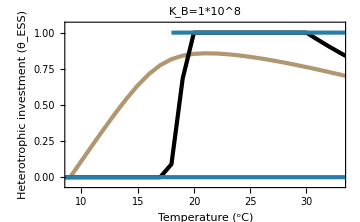
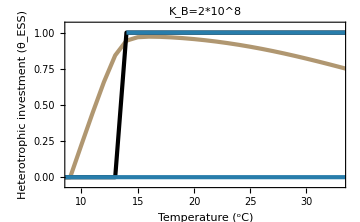
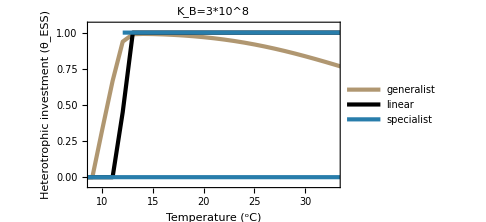

```mathematica
ones=Table[1,100];
zeros=Table[0,100];
List[Subscript[K, B]=1 10^8;Subscript[I, in]=150;
ListPlot[{makeθListGen[]//Flatten,makeθListLin[]//Flatten,makeθListSpec[][[1]][[1]],makeθListSpec[][[1]][[2]]},Joined->True,PlotRange->{{9,33},{-.05,1.05}},PlotStyle->{{RGBColor["#B09771"],AbsoluteThickness[3]}, {Black,AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]}},Frame->True,ImageSize->Medium,FrameLabel->{Style["Temperature (^oC)",12,Black],Style["Heterotrophic investment (θ_ESS)",12,Black]},FrameTicksStyle->Directive[Black,12],PlotLabel->Style["K_B=1*10^8",12,Black]],Subscript[K, B]=2 10^8;Subscript[I, in]=150;
ListPlot[{makeθListGen[]//Flatten,makeθListLin[]//Flatten,makeθListSpec[][[1]][[1]],makeθListSpec[][[1]][[2]]},Joined->True,PlotRange->{{9,33},{-.05,1.05}},PlotStyle->{{RGBColor["#B09771"],AbsoluteThickness[3]}, {Black,AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]}},Frame->True,ImageSize->Medium,FrameLabel->{Style["Temperature (^oC)",12,Black],Style["Heterotrophic investment (θ_ESS)",12,Black]},FrameTicksStyle->Directive[Black,12],PlotLabel->Style["K_B=2*10^8",12,Black]],Subscript[K, B]=3 10^8;Subscript[I, in]=150;
ListPlot[{makeθListGen[]//Flatten,makeθListLin[]//Flatten,makeθListSpec[][[1]][[1]],makeθListSpec[][[1]][[2]]},Joined->True,PlotRange->{{9,33},{-.05,1.05}},PlotStyle->{{RGBColor["#B09771"],AbsoluteThickness[3]}, {Black,AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]}},Frame->True,ImageSize->Medium,FrameLabel->{Style["Temperature (^oC)",12,Black],Style["Heterotrophic investment (θ_ESS)",12,Black]},PlotLegends->{"generalist", "linear","specialist"},FrameTicksStyle->Directive[Black,12],PlotLabel->Style["K_B=3*10^8",12,Black]]]
```

## Exponential temperature dependence

Table::nliter: Non-list iterator θESSspec0 at position 2 does not evaluate to a real numeric value.

General::stop: Further output of Table::nliter will be suppressed during this calculation.

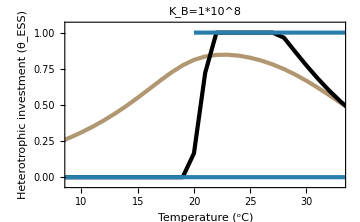
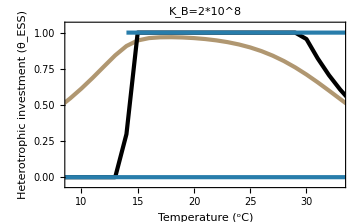
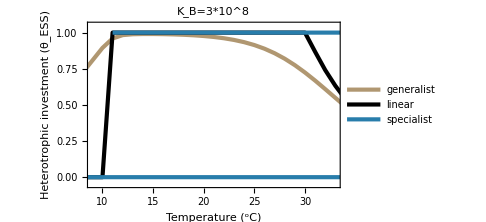

```mathematica
List[Subscript[K, B]=1 10^8;Subscript[I, in]=150;
ListPlot[{makeθListGenExp[]//Flatten,makeθListLinExp[]//Flatten,makeθListSpecExp[][[1]][[1]],makeθListSpecExp[][[1]][[2]]},Joined->True,PlotRange->{{9,33},{-.05,1.05}},PlotStyle->{{RGBColor["#B09771"],AbsoluteThickness[3]}, {Black,AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]}},Frame->True,ImageSize->Medium,FrameLabel->{Style["Temperature (^oC)",12,Black],Style["Heterotrophic investment (θ_ESS)",12,Black]},FrameTicksStyle->Directive[Black,12],PlotLabel->Style["K_B=1*10^8",12,Black]],Subscript[K, B]=2 10^8;Subscript[I, in]=150;
ListPlot[{makeθListGenExp[]//Flatten,makeθListLinExp[]//Flatten,makeθListSpecExp[][[1]][[1]],makeθListSpecExp[][[1]][[2]]},Joined->True,PlotRange->{{9,33},{-.05,1.05}},PlotStyle->{{RGBColor["#B09771"],AbsoluteThickness[3]}, {Black,AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]}},Frame->True,ImageSize->Medium,FrameLabel->{Style["Temperature (^oC)",12,Black],Style["Heterotrophic investment (θ_ESS)",12,Black]},FrameTicksStyle->Directive[Black,12],PlotLabel->Style["K_B=2*10^8",12,Black]],Subscript[K, B]=3 10^8;Subscript[I, in]=150;
ListPlot[{makeθListGenExp[]//Flatten,makeθListLinExp[]//Flatten,makeθListSpecExp[][[1]][[1]],makeθListSpecExp[][[1]][[2]]},Joined->True,PlotRange->{{9,33},{-.05,1.05}},PlotStyle->{{RGBColor["#B09771"],AbsoluteThickness[3]}, {Black,AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]},{RGBColor["#287DAB"],AbsoluteThickness[3]}},Frame->True,ImageSize->Medium,FrameLabel->{Style["Temperature (^oC)",12,Black],Style["Heterotrophic investment (θ_ESS)",12,Black]},PlotLegends->{"generalist", "linear","specialist"},FrameTicksStyle->Directive[Black,12],PlotLabel->Style["K_B=3*10^8",12,Black]]]
```

# Pairwise invasibility plots

## K_B=1*10^8, I_in=100

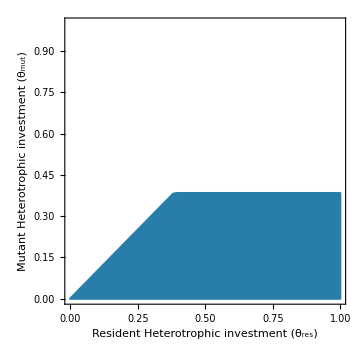
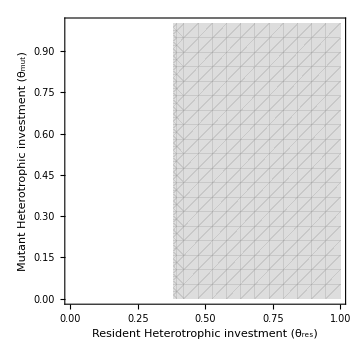
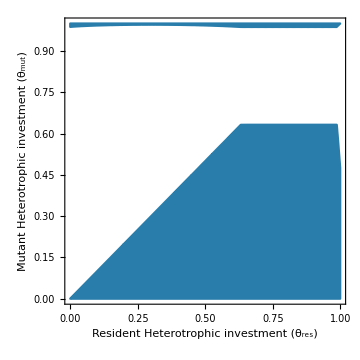
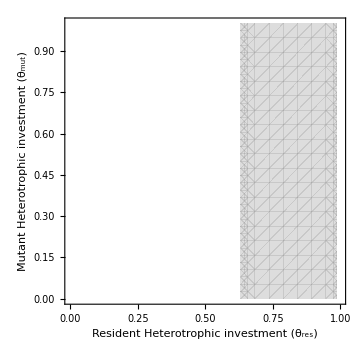
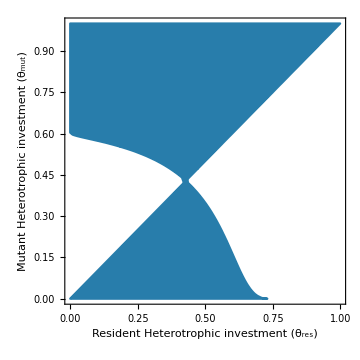
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

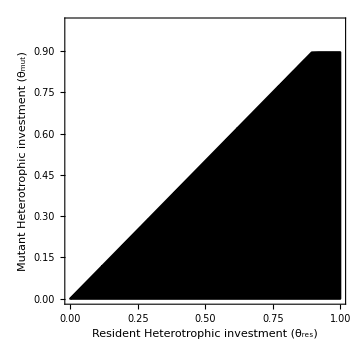
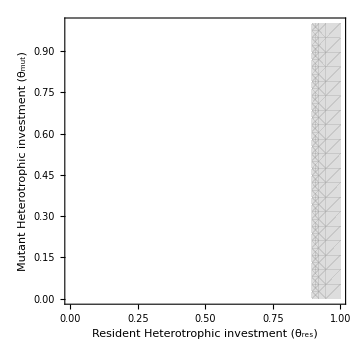
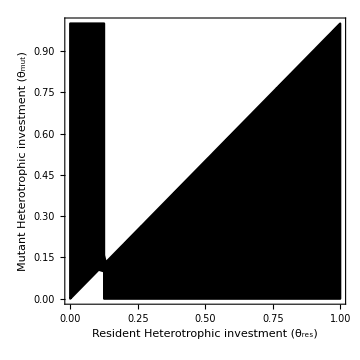
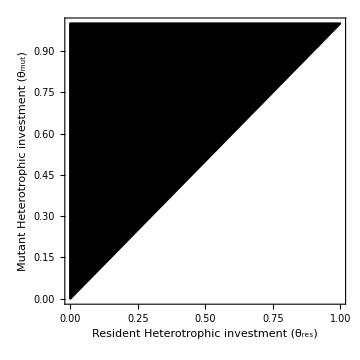
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

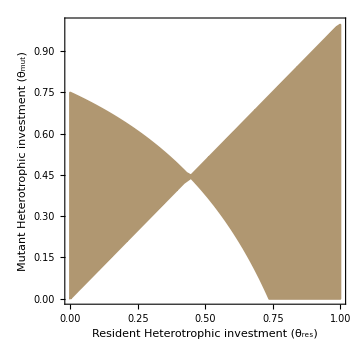
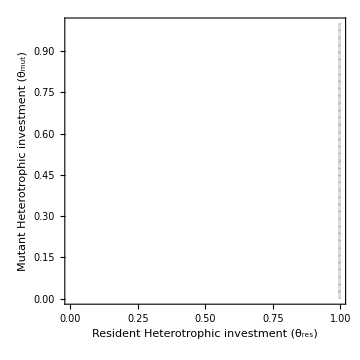
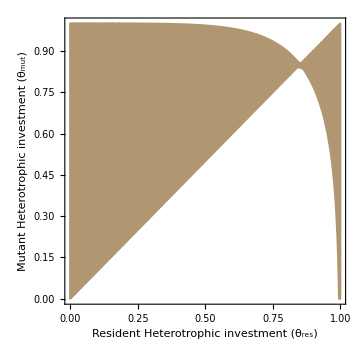
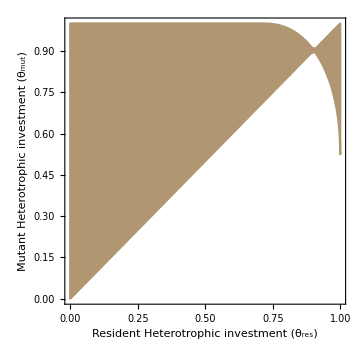
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
Subscript[K, B]=1 10^8;Subscript[I, in]=100;
Quiet[List[Overlay[{MakePIP[-1,T0,RGBColor["#287DAB"]],MakePIPNV[-1,T0,Lighter[Gray]]}],Overlay[{MakePIP[-1,T0+5,RGBColor["#287DAB"]],MakePIPNV[-1,T0+5,Lighter[Gray]]}],Overlay[{MakePIP[-1,T0+10,RGBColor["#287DAB"]],MakePIPNV[-1,T0+10,Lighter[Gray]]}]]]
Quiet[List[Overlay[{MakePIP[0,T0,Black],MakePIPNV[0,T0,Lighter[Gray]]}],Overlay[{MakePIP[0,T0+5,Black],MakePIPNV[0,T0+5,Lighter[Gray]]}],Overlay[{MakePIP[0,T0+10,Black],MakePIPNV[0,T0+10,Lighter[Gray]]}]]](*linear*)
Quiet[List[Overlay[{MakePIP[1,T0,RGBColor["#B09771"]],MakePIPNV[1,T0,Lighter[Gray]]}],Overlay[{MakePIP[1,T0+5,RGBColor["#B09771"]],MakePIPNV[1,T0+5,Lighter[Gray]]}],Overlay[{MakePIP[1,T0+10,RGBColor["#B09771"]],MakePIPNV[1,T0+10,Lighter[Gray]]}]]]
(*generalist*)
```

## K_B=2*10^8, I_in=100

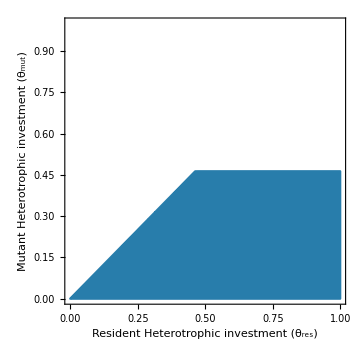
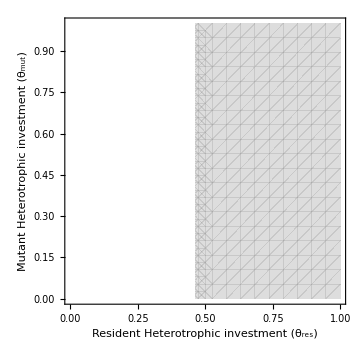
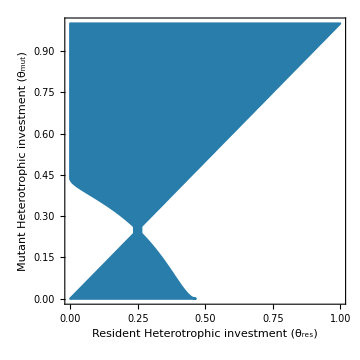
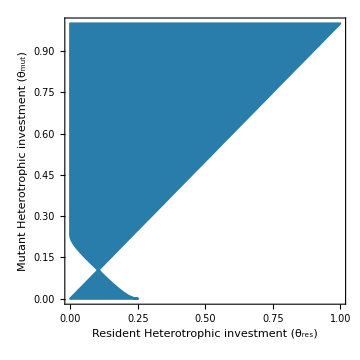
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

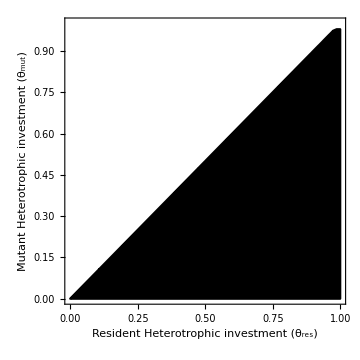
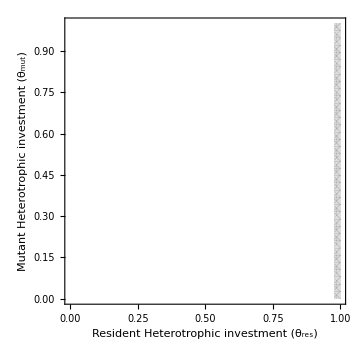
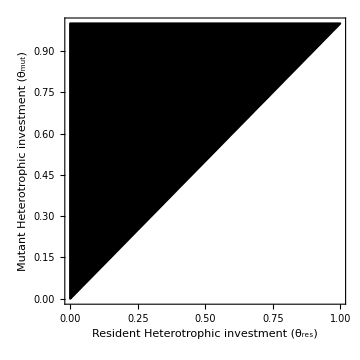
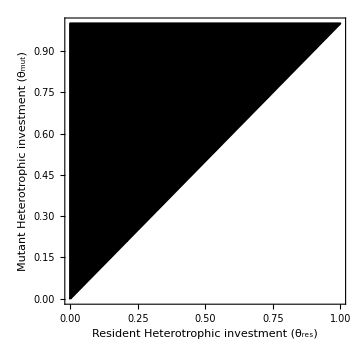
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

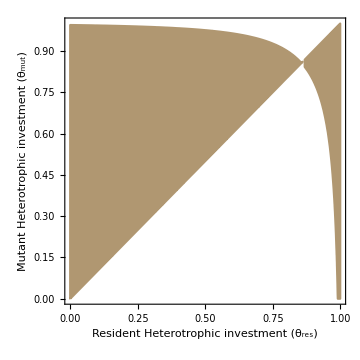
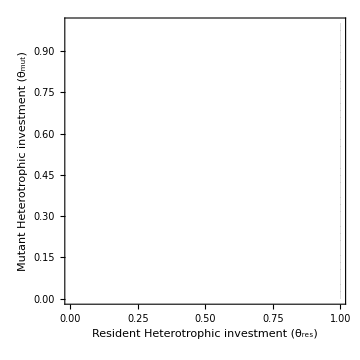
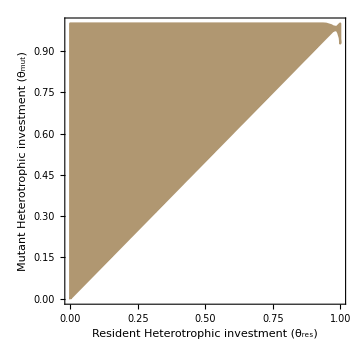
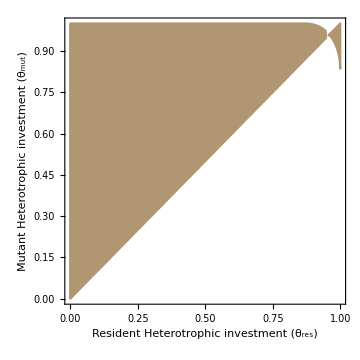
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
Subscript[K, B]=2 10^8;Subscript[I, in]=100;
Quiet[List[Overlay[{MakePIP[-1,T0,RGBColor["#287DAB"]],MakePIPNV[-1,T0,Lighter[Gray]]}],Overlay[{MakePIP[-1,T0+5,RGBColor["#287DAB"]],MakePIPNV[-1,T0+5,Lighter[Gray]]}],Overlay[{MakePIP[-1,T0+10,RGBColor["#287DAB"]],MakePIPNV[-1,T0+10,Lighter[Gray]]}]]]
Quiet[List[Overlay[{MakePIP[0,T0,Black],MakePIPNV[0,T0,Lighter[Gray]]}],Overlay[{MakePIP[0,T0+5,Black],MakePIPNV[0,T0+5,Lighter[Gray]]}],Overlay[{MakePIP[0,T0+10,Black],MakePIPNV[0,T0+10,Lighter[Gray]]}]]](*linear*)
Quiet[List[Overlay[{MakePIP[1,T0,RGBColor["#B09771"]],MakePIPNV[1,T0,Lighter[Gray]]}],Overlay[{MakePIP[1,T0+5,RGBColor["#B09771"]],MakePIPNV[1,T0+5,Lighter[Gray]]}],Overlay[{MakePIP[1,T0+10,RGBColor["#B09771"]],MakePIPNV[1,T0+10,Lighter[Gray]]}]]]
(*generalist*)
```

## K_B=3*10^8, I_in=100

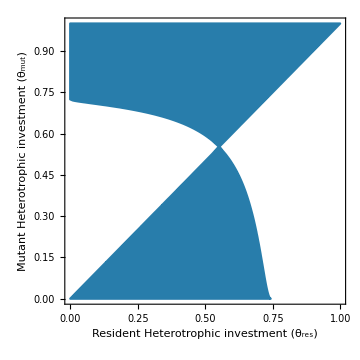
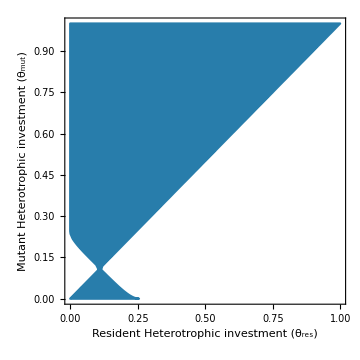
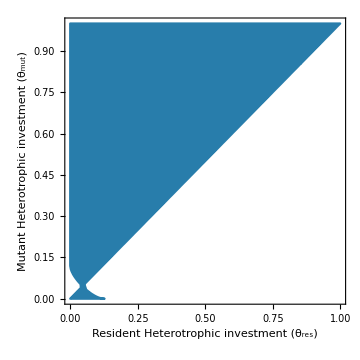
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

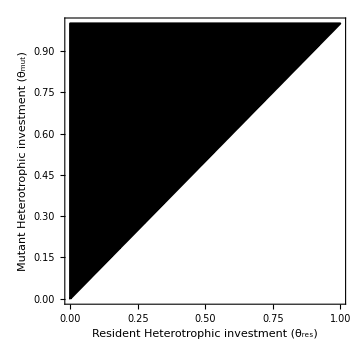
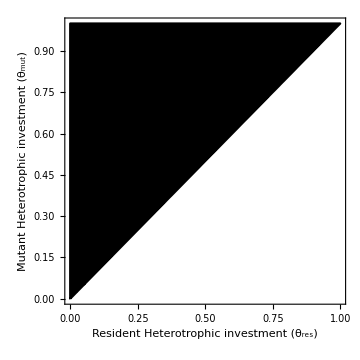
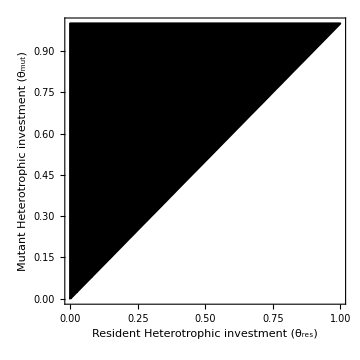
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

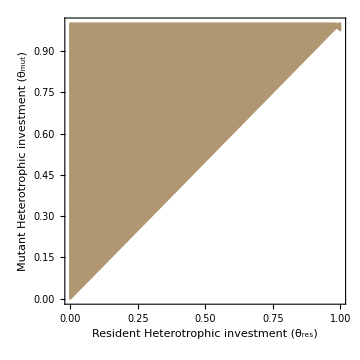
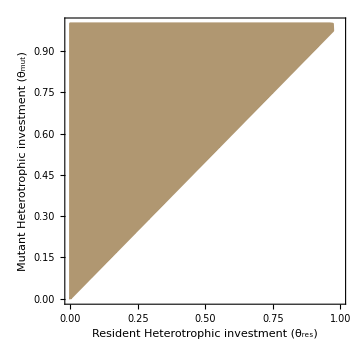
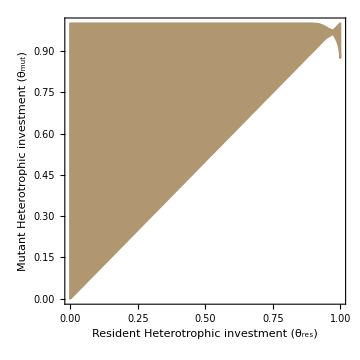
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
Subscript[K, B]=3 10^8;Subscript[I, in]=100;
Quiet[List[Overlay[{MakePIP[-1,T0,RGBColor["#287DAB"]],MakePIPNV[-1,T0,Lighter[Gray]]}],Overlay[{MakePIP[-1,T0+5,RGBColor["#287DAB"]],MakePIPNV[-1,T0+5,Lighter[Gray]]}],Overlay[{MakePIP[-1,T0+10,RGBColor["#287DAB"]],MakePIPNV[-1,T0+10,Lighter[Gray]]}]]]
Quiet[List[Overlay[{MakePIP[0,T0,Black],MakePIPNV[0,T0,Lighter[Gray]]}],Overlay[{MakePIP[0,T0+5,Black],MakePIPNV[0,T0+5,Lighter[Gray]]}],Overlay[{MakePIP[0,T0+10,Black],MakePIPNV[0,T0+10,Lighter[Gray]]}]]](*linear*)
Quiet[List[Overlay[{MakePIP[1,T0,RGBColor["#B09771"]],MakePIPNV[1,T0,Lighter[Gray]]}],Overlay[{MakePIP[1,T0+5,RGBColor["#B09771"]],MakePIPNV[1,T0+5,Lighter[Gray]]}],Overlay[{MakePIP[1,T0+10,RGBColor["#B09771"]],MakePIPNV[1,T0+10,Lighter[Gray]]}]]]
(*generalist*)
```

## K_B=1*10^8, I_in=150

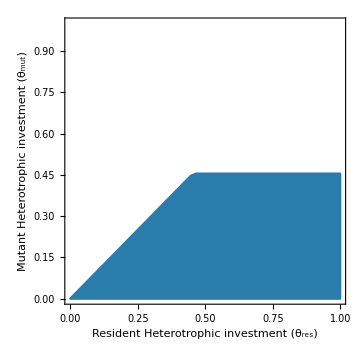
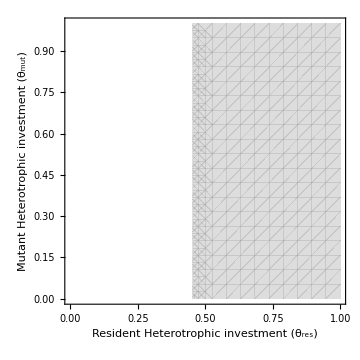
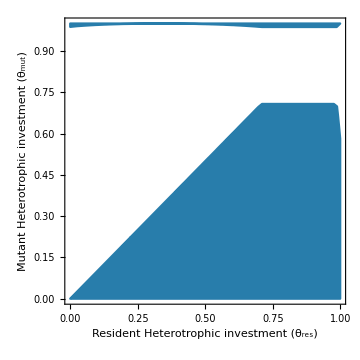
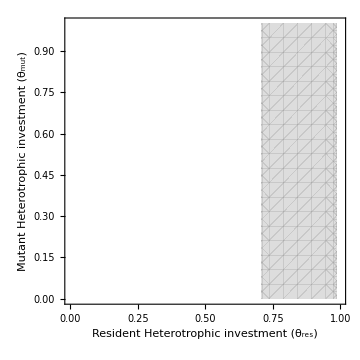
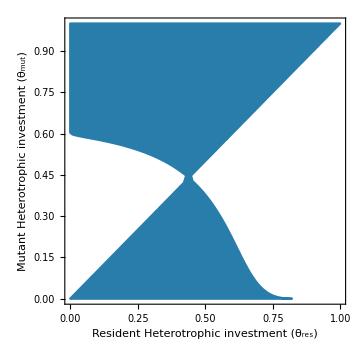
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

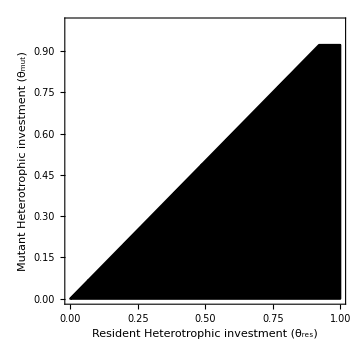
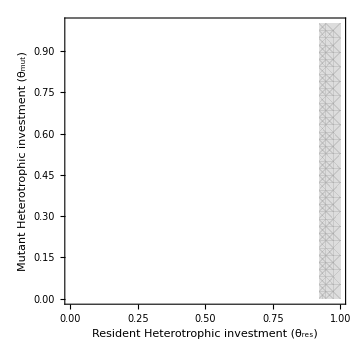
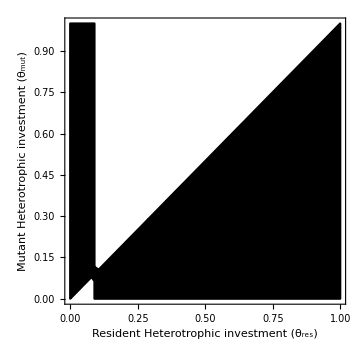
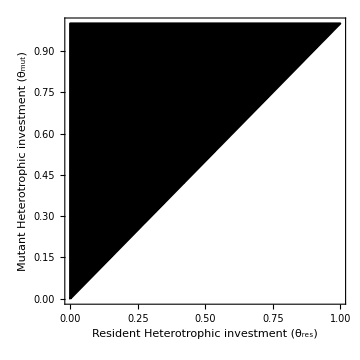
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

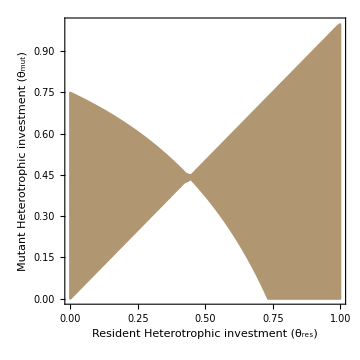
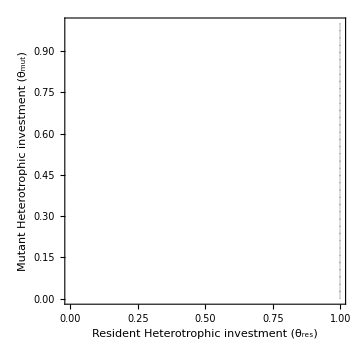
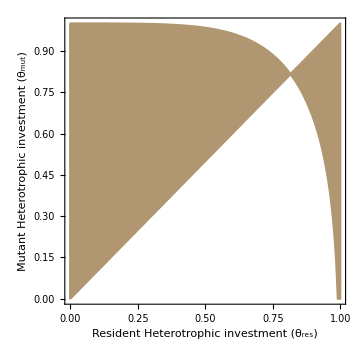
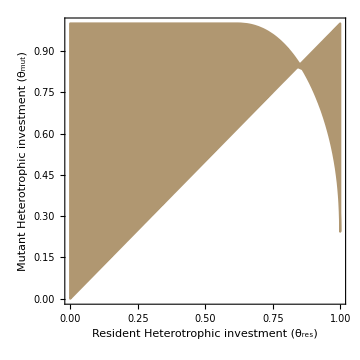
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
Subscript[K, B]=1 10^8;Subscript[I, in]=150;
Quiet[List[Overlay[{MakePIP[-1,T0,RGBColor["#287DAB"]],MakePIPNV[-1,T0,Lighter[Gray]]}],Overlay[{MakePIP[-1,T0+5,RGBColor["#287DAB"]],MakePIPNV[-1,T0+5,Lighter[Gray]]}],Overlay[{MakePIP[-1,T0+10,RGBColor["#287DAB"]],MakePIPNV[-1,T0+10,Lighter[Gray]]}]]]
Quiet[List[Overlay[{MakePIP[0,T0,Black],MakePIPNV[0,T0,Lighter[Gray]]}],Overlay[{MakePIP[0,T0+5,Black],MakePIPNV[0,T0+5,Lighter[Gray]]}],Overlay[{MakePIP[0,T0+10,Black],MakePIPNV[0,T0+10,Lighter[Gray]]}]]](*linear*)
Quiet[List[Overlay[{MakePIP[1,T0,RGBColor["#B09771"]],MakePIPNV[1,T0,Lighter[Gray]]}],Overlay[{MakePIP[1,T0+5,RGBColor["#B09771"]],MakePIPNV[1,T0+5,Lighter[Gray]]}],Overlay[{MakePIP[1,T0+10,RGBColor["#B09771"]],MakePIPNV[1,T0+10,Lighter[Gray]]}]]]
(*generalist*)
```

## K_B=2*10^8, I_in=150

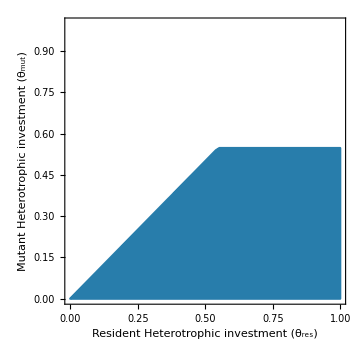
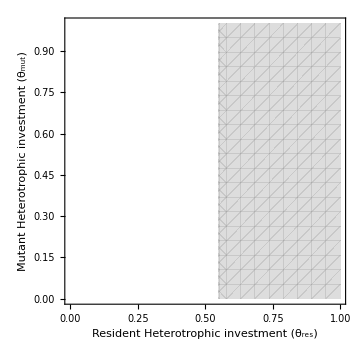
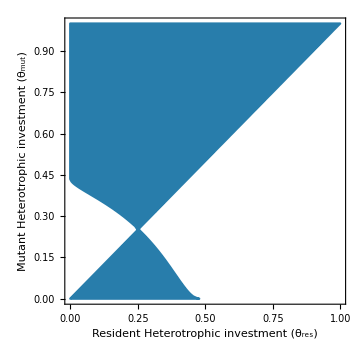
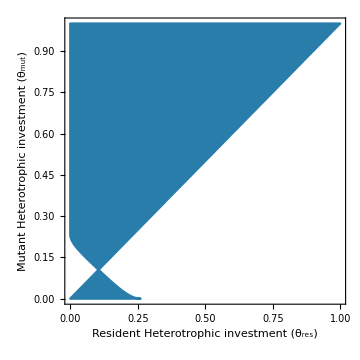
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

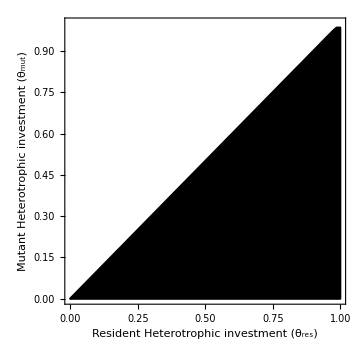
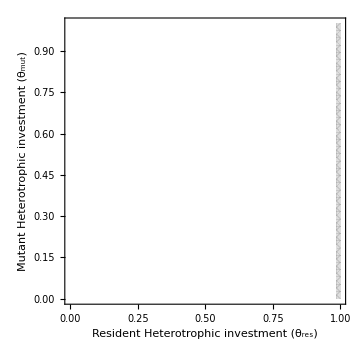
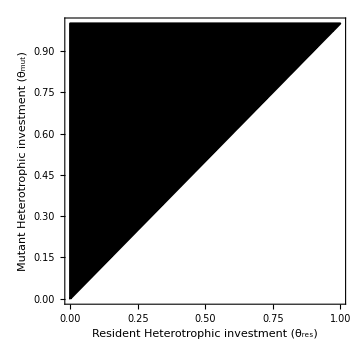
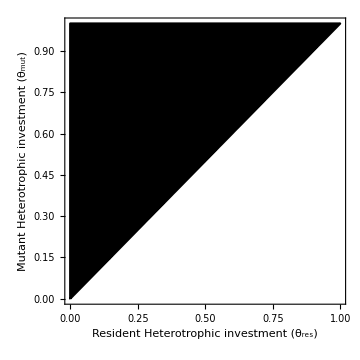
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

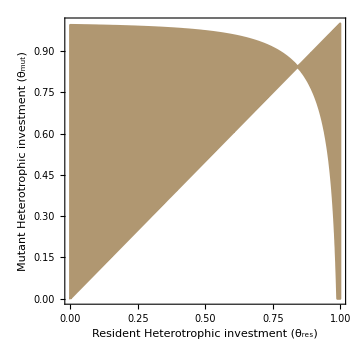
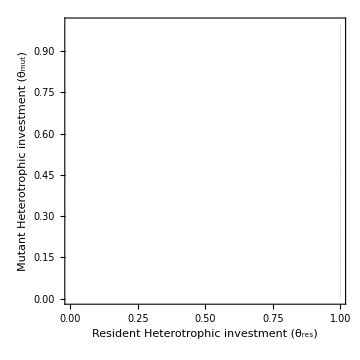
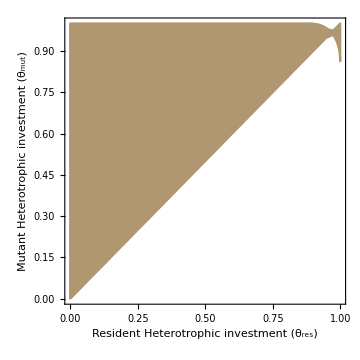
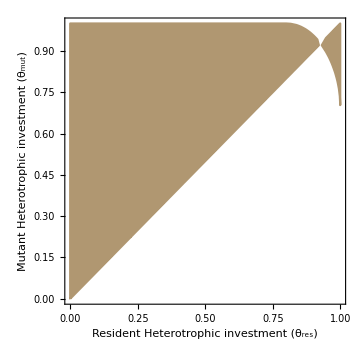
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
Subscript[K, B]=2 10^8;Subscript[I, in]=150;
Quiet[List[Overlay[{MakePIP[-1,T0,RGBColor["#287DAB"]],MakePIPNV[-1,T0,Lighter[Gray]]}],Overlay[{MakePIP[-1,T0+5,RGBColor["#287DAB"]],MakePIPNV[-1,T0+5,Lighter[Gray]]}],Overlay[{MakePIP[-1,T0+10,RGBColor["#287DAB"]],MakePIPNV[-1,T0+10,Lighter[Gray]]}]]]
Quiet[List[Overlay[{MakePIP[0,T0,Black],MakePIPNV[0,T0,Lighter[Gray]]}],Overlay[{MakePIP[0,T0+5,Black],MakePIPNV[0,T0+5,Lighter[Gray]]}],Overlay[{MakePIP[0,T0+10,Black],MakePIPNV[0,T0+10,Lighter[Gray]]}]]](*linear*)
Quiet[List[Overlay[{MakePIP[1,T0,RGBColor["#B09771"]],MakePIPNV[1,T0,Lighter[Gray]]}],Overlay[{MakePIP[1,T0+5,RGBColor["#B09771"]],MakePIPNV[1,T0+5,Lighter[Gray]]}],Overlay[{MakePIP[1,T0+10,RGBColor["#B09771"]],MakePIPNV[1,T0+10,Lighter[Gray]]}]]]
(*generalist*)
```

## K_B=3*10^8, I_in=150

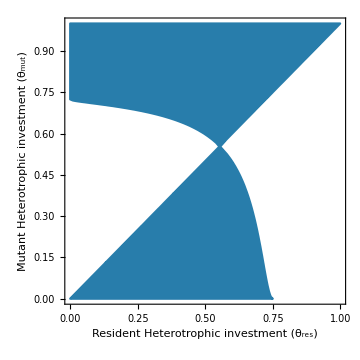
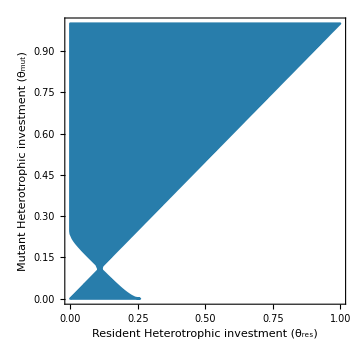
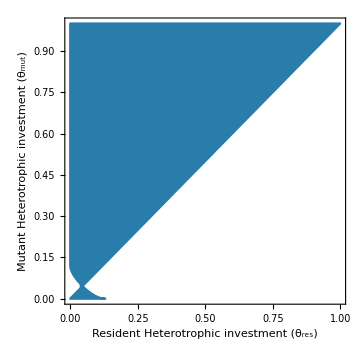
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

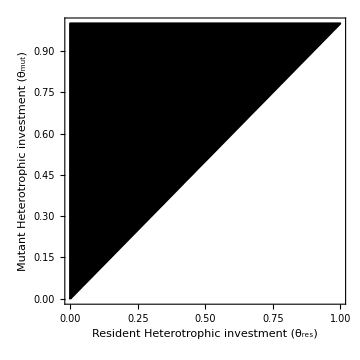
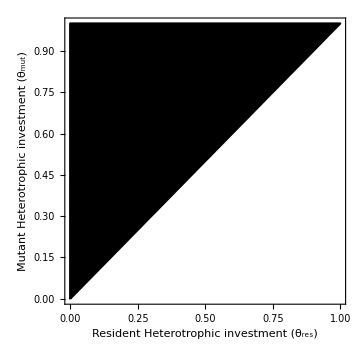
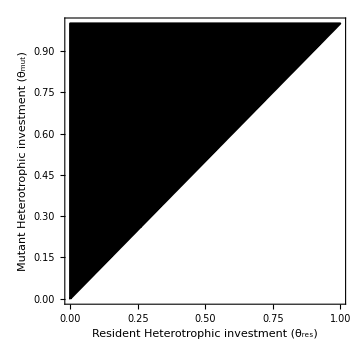
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

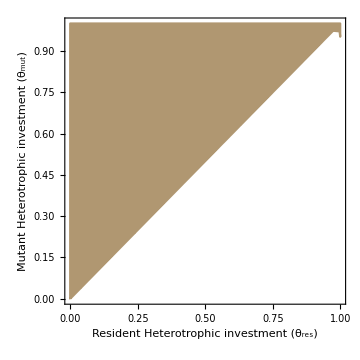
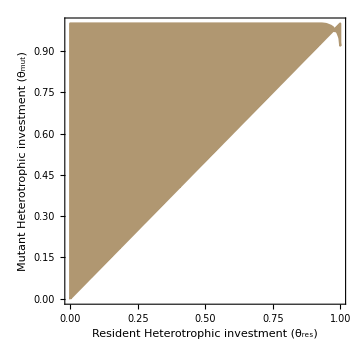
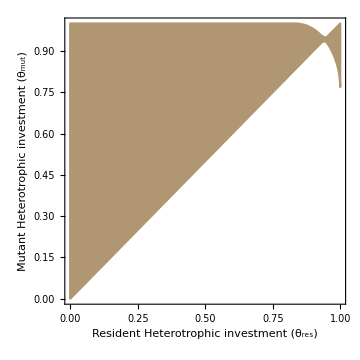
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
Subscript[K, B]=3 10^8;Subscript[I, in]=150;
Quiet[List[Overlay[{MakePIP[-1,T0,RGBColor["#287DAB"]],MakePIPNV[-1,T0,Lighter[Gray]]}],Overlay[{MakePIP[-1,T0+5,RGBColor["#287DAB"]],MakePIPNV[-1,T0+5,Lighter[Gray]]}],Overlay[{MakePIP[-1,T0+10,RGBColor["#287DAB"]],MakePIPNV[-1,T0+10,Lighter[Gray]]}]]]
Quiet[List[Overlay[{MakePIP[0,T0,Black],MakePIPNV[0,T0,Lighter[Gray]]}],Overlay[{MakePIP[0,T0+5,Black],MakePIPNV[0,T0+5,Lighter[Gray]]}],Overlay[{MakePIP[0,T0+10,Black],MakePIPNV[0,T0+10,Lighter[Gray]]}]]](*linear*)
Quiet[List[Overlay[{MakePIP[1,T0,RGBColor["#B09771"]],MakePIPNV[1,T0,Lighter[Gray]]}],Overlay[{MakePIP[1,T0+5,RGBColor["#B09771"]],MakePIPNV[1,T0+5,Lighter[Gray]]}],Overlay[{MakePIP[1,T0+10,RGBColor["#B09771"]],MakePIPNV[1,T0+10,Lighter[Gray]]}]]]
(*generalist*)
```

# C-cycling related figures (Dashed - genetically static, Solid - evolving)

## K_B=1*10^8, I_in=100

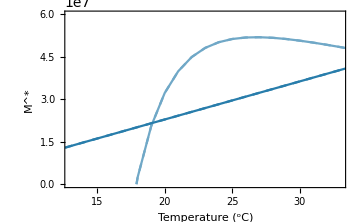
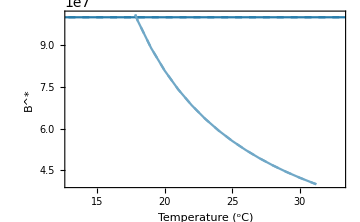
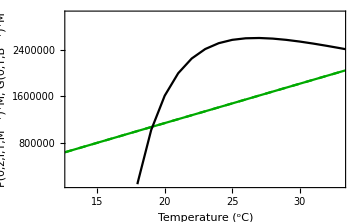

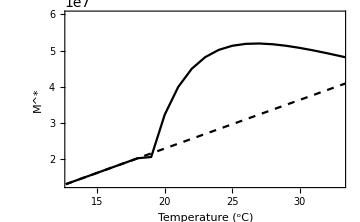
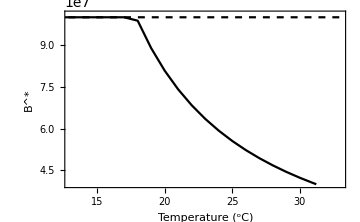
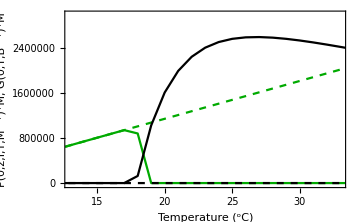

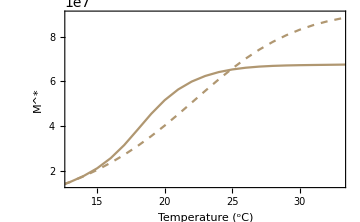
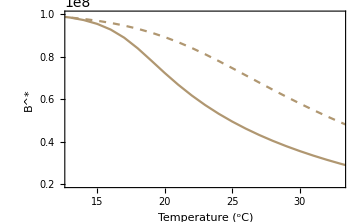

```mathematica
Subscript[K, B]=1 10^8;Subscript[I, in]=100;
Quiet[Ccyclingspec[-1,0,6 10^7 ,4 10^7,1.01 10^8,10^5,3 10^6]]
Quiet[Ccycling[0,1.3 10^7,6 10^7 ,4 10^7,1.01 10^8,-20000,3 10^6]]
Quiet[Ccycling[1,1.4 10^7,9 10^7 ,2 10^7,10 10^7,0,3 10^6]]
```

## K_B=2*10^8, I_in=100

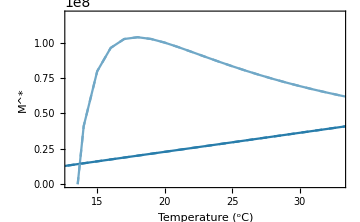
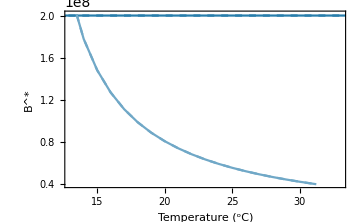
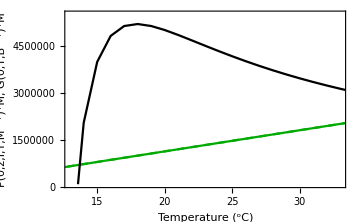

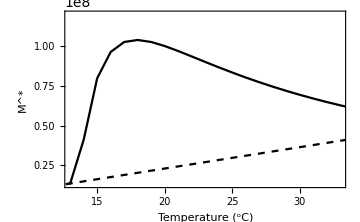
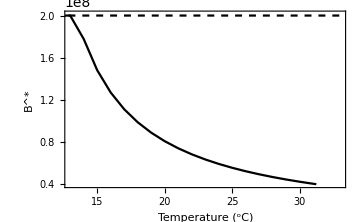
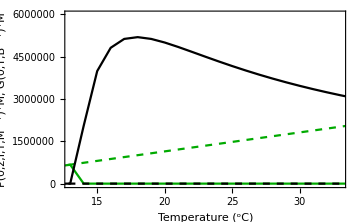

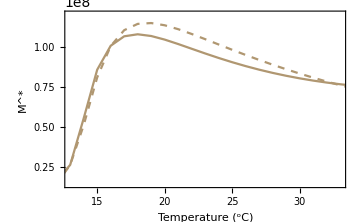
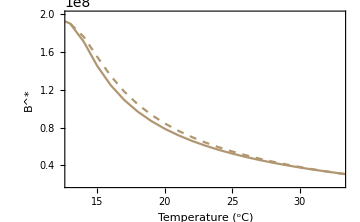

```mathematica
Subscript[K, B]=2 10^8;Subscript[I, in]=100;
Quiet[Ccyclingspec[-1,0,1.2 10^8 ,4 10^7,2.01 10^8,10^5,5.5 10^6]]
Quiet[Ccycling[0,1.3 10^7,1.2 10^8 ,4 10^7,2.01 10^8,-20000,6 10^6]]
Quiet[Ccycling[1,1.4 10^7,1.2 10^8 ,2 10^7,2 10^8,0,6 10^6]]
```

## K_B=3*10^8, I_in=100

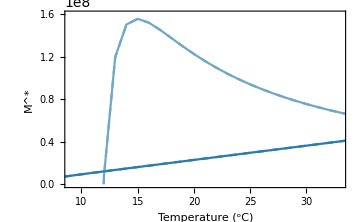
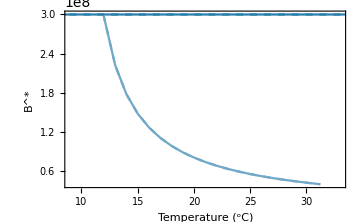
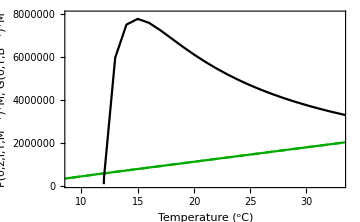

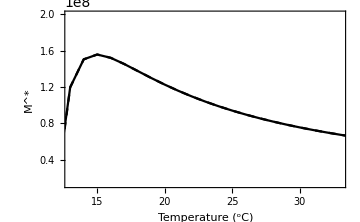
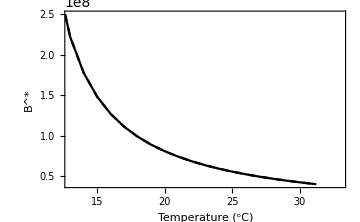
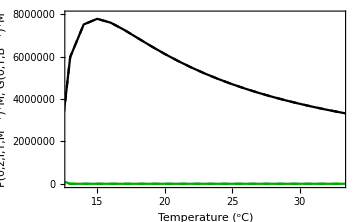

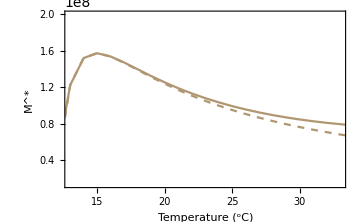
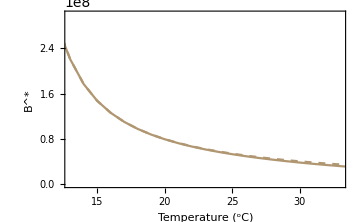

```mathematica
Subscript[K, B]=3 10^8;Subscript[I, in]=100;
Quiet[Ccyclingspec[-1,0,1.6 10^8 ,4 10^7,3 10^8,10^5,8 10^6]]
Quiet[Ccycling[0,1.3 10^7,2 10^8 ,4 10^7,2.5 10^8,-20000,8 10^6]]
Quiet[Ccycling[1,1.4 10^7,2 10^8 ,0,3 10^8,0,8 10^6]]
```

## K_B=1*10^8, I_in=150

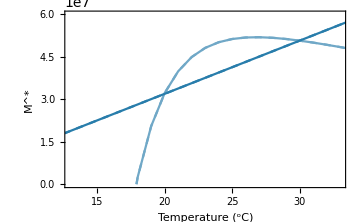
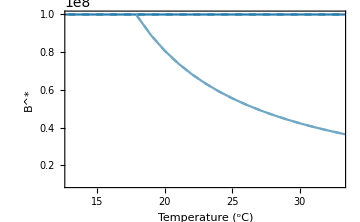
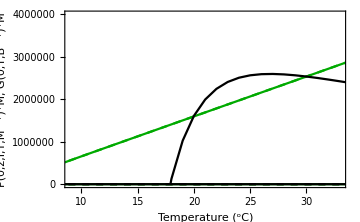

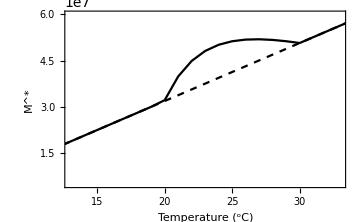
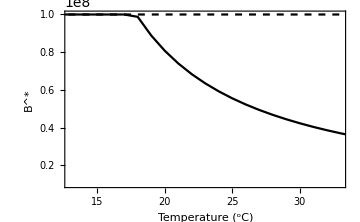
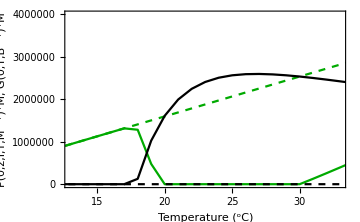

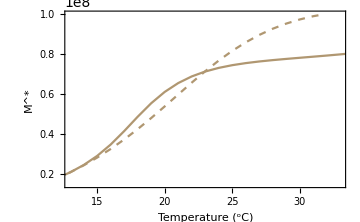
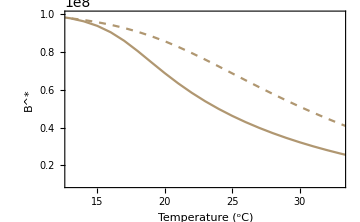

```mathematica
Subscript[K, B]=1 10^8;Subscript[I, in]=150;
Quiet[Ccyclingspec[-1,0,6.0 10^7 ,1 10^7,1 10^8,0,4 10^6]]
Quiet[Ccycling[0,.5 10^7,6.0 10^7 ,1 10^7,1 10^8,0,4 10^6]]
Quiet[Ccycling[1,1.5 10^7,1 10^8 ,1 10^7,1 10^8,0,3 10^6]]
```

## K_B=2*10^8, I_in=150

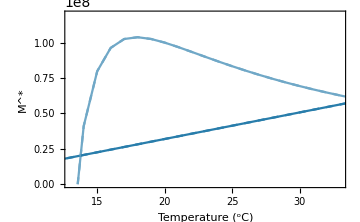
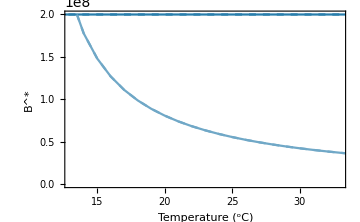
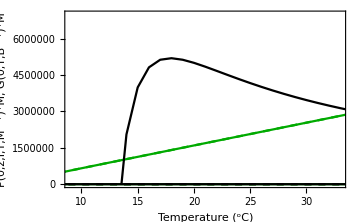

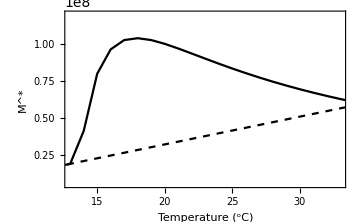
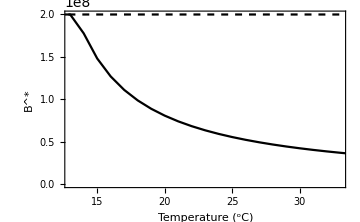
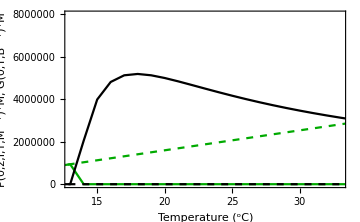

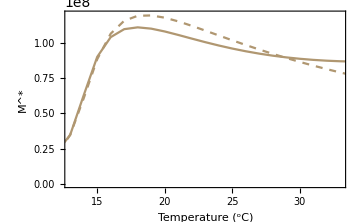
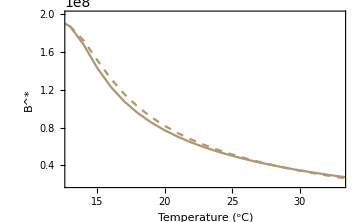

```mathematica
Subscript[K, B]=2 10^8;Subscript[I, in]=150;
Quiet[Ccyclingspec[-1,0,1.2 10^8 ,0,2 10^8,0,7 10^6]]
Quiet[Ccycling[0,.5 10^7,1.2 10^8 ,0,2 10^8,0,8 10^6]]
Quiet[Ccycling[1,0 10^7,1.2 10^8 ,2 10^7,2 10^8,0,8 10^6]]
```

## K_B=3*10^8, I_in=150

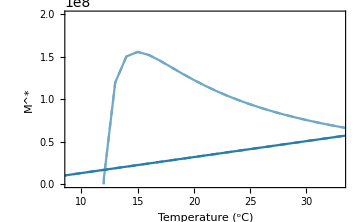
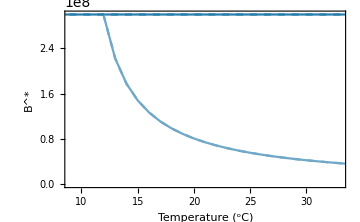
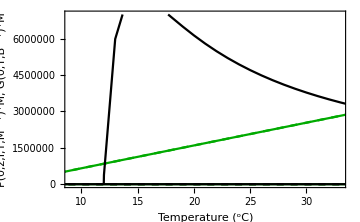

{{-Graphics-,-Graphics-,-Graphics-}}

{{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Subscript[K, B]=3 10^8;Subscript[I, in]=150;
Quiet[Ccyclingspec[-1,0 ,2 10^8 ,0 10^7,3 10^8,0,7 10^6]]
Quiet[Ccycling[0,0 10^7,2 10^8 ,0 10^7,2.5 10^8,0,8 10^6]]
Quiet[Ccycling[1,0 10^7,2 10^8 ,2 10^7,2.5 10^8,0,8 10^6]]
```